# Convolución de dos variables discretas

## Convolución de dos variables Poisson X\[Distributed]P[2], Y\[Distributed]P[3]

```mathematica
pdf1 = PDF[PoissonDistribution[2], x]
```

Piecewise[{{2^x/(ⅇ^2 x!), x≥0}, {0, True}}]

```mathematica
pdf2 = PDF[PoissonDistribution[3], x]
```

Piecewise[{{3^x/(ⅇ^3 x!), x≥0}, {0, True}}]

Función de probabilidad de la convolución

```mathematica
fconvolucion[z_] := DiscreteConvolve[pdf1, pdf2, x, z]
```

```mathematica
fconvolucion[z]
```

Piecewise[{{5^z/(ⅇ^5 z!), z≥0}, {0, True}}]

Construcción del modelo a partir de la función de probabilidad

```mathematica
Convolucion1 = ProbabilityDistribution[fconvolucion[z], {z, 0, ∞, 1}] (*'escape' inf -> me pone infinito*)
```

ProbabilityDistribution[Piecewise[{{5^x/(ⅇ^5 x!), x≥0}, {0, True}}],{x,0,∞,1}]

Construcción del modelo directamente

```mathematica
TransformedDistribution[X1+X2, {X1\[Distributed]PoissonDistribution[a], X2 \[Distributed] PoissonDistribution[b]}] (*la suma de Poisson es Poisson*)
```

PoissonDistribution[a+b]

# Convolución de dos variables continuas

## Convolución de una variable uniforme X\[Distributed]𝒰[-1, 1] con una triangular Y\[Distributed]𝒯[-2, 2]

```mathematica
pdf3 = PDF[UniformDistribution[{-1, 1}], x] (*escape + 'dist' -> \[Distributed]*)
```

Piecewise[{{1/2, -1≤x≤1}, {0, True}}]

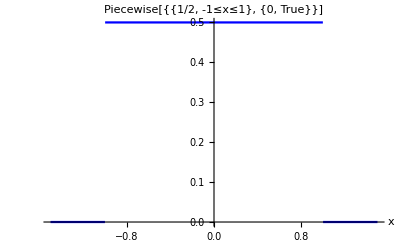

```mathematica
Plot[pdf3, {x, -1.5, 1.5}, PlotRange->{{-1.5, 1.5}, Automatic}, AxesLabel->{x, pdf3}, PlotStyle->Blue]
```

```mathematica
pdf4 = PDF[TriangularDistribution[{-2, 2}], x]
```

Piecewise[{{(2+x)/4, -2≤x≤0}, {(2-x)/4, 0<x≤2}, {0, True}}]

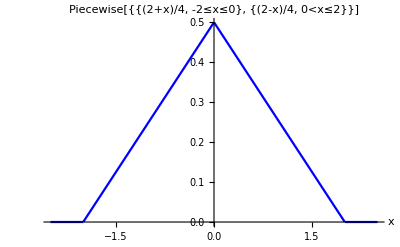

```mathematica
Plot[pdf4, {x, -2.5, 2.5}, PlotRange->{{-2.5, 2.5}, Automatic}, AxesLabel->{x, pdf4}, PlotStyle->Blue]
```

Función de densidad de la convolución

```mathematica
fconvolucion2[z_] := Convolve[pdf3, pdf4, x, z]
```

```mathematica
fconvolucion2[z]
```

Piecewise[{{1/8 (3-z^2), -1<z≤1}, {1/16 (-3+z)^2, 1<z<3}, {1/16 (3+z)^2, -3<z≤-1}, {0, True}}]

Construcción del modelo a partir de la función de densidad

```mathematica
Convolucion2=ProbabilityDistribution[Convolve[pdf3, pdf4, x, z], {z, -∞, ∞}]
```

ProbabilityDistribution[Piecewise[{{1/8 (3-x^2), -1<x≤1}, {1/16 (-3+x)^2, 1<x<3}, {1/16 (3+x)^2, -3<x≤-1}, {0, True}}],{x,-∞,∞}]

```mathematica
Z[x_] := CDF[Convolucion2, x]
```

```mathematica
Z[x]
```

Piecewise[{{1, x≥3}, {1/24 (12+9 x-x^3), -1<x≤1}, {1/48 (21+27 x-9 x^2+x^3), 1<x<3}, {1/48 (27+27 x+9 x^2+x^3), -3<x≤-1}, {0, True}}]

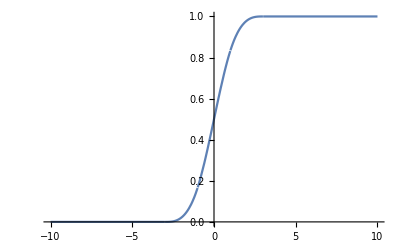

```mathematica
Plot[Z[x], {x, -10, 10}]
```

Función de distribución de la convolución

```mathematica
fdis4 = CDF[TriangularDistribution[{-2, 2}], x]
```

Piecewise[{{1/8 (2+x)^2, -2≤x≤0}, {1-1/8 (2-x)^2, 0<x≤2}, {1, x>2}, {0, True}}]

```mathematica
Convolve[pdf3, fdis4, x, z]
```

Piecewise[{{1, z>3}, {1/2 (-1+z), z==3}, {1/48 (3+z)^3, -3<z≤-1}, {1/24 (12+9 z-z^3), -1<z<1}, {1/48 (17+21 z+3 z^2-z^3), z==1}, {1/48 (21+27 z-9 z^2+z^3), 1<z<3}, {0, True}}]

```mathematica
Simplify[%]
```

Piecewise[{{1, z≥3}, {1/48 (3+z)^3, -3<z≤-1}, {1/24 (12+9 z-z^3), -1<z≤1}, {1/48 (21+27 z-9 z^2+z^3), 1<z<3}, {0, True}}]

Función de distribución de la convolución

```mathematica
Probability[X1+X2<=z, {X1 \[Distributed]UniformDistribution[{-1, 1}], X2 \[Distributed] TriangularDistribution[{-2, 2}]}]
```

Piecewise[{{1, z>3}, {1/48 (3+z)^3, -3≤z≤-1}, {1/24 (12+9 z-z^3), -1<z≤1}, {1/48 (21+27 z-9 z^2+z^3), 1<z≤3}, {0, True}}]

Construcción del modelo a partir de la función de distribución

```mathematica
Convolucion3 = ProbabilityDistribution[{"CDF", Convolve[pdf3, fdis4, x, z]} , {z, -∞, ∞}]
```

ProbabilityDistribution[Piecewise[{{1/2, x==3}, {1/16 (3+x)^2, -3<x≤-1}, {1/24 (9-3 x^2), -1<x<1}, {1/48 (21+6 x-3 x^2), x==1}, {1/48 (27-18 x+3 x^2), 1<x<3}, {0, True}}],{x,-∞,∞}]

```mathematica
CDF[Convolucion3, x]
```

Piecewise[{{5/6, x==1}, {1, x≥3}, {1/24 (12+9 x-x^3), -1<x<1}, {1/48 (21+27 x-9 x^2+x^3), 1<x<3}, {1/48 (27+27 x+9 x^2+x^3), -3<x≤-1}, {0, True}}]

```mathematica
Simplify[%]
```

Piecewise[{{1/24 (12+9 x-x^3), -1<x≤1}, {1, x≥3}, {1/48 (21+27 x-9 x^2+x^3), 1<x<3}, {1/48 (3+x)^3, -3<x≤-1}, {0, True}}]

# Convolución de una continua con una mixta

## Convolución de una variable mixta con función de distribución dada F(x) = {0 si x < -2, (x+2)/4 si - 2 ≤ x < 1, 1 si x ≥ 1;} y una variable con distribución uniforme Y\[Distributed]𝒰[0, 2]

Construcción de un modelo mixto a partir de la función de distribución
La variable X es una mixtura de una distribución uniforme en [-2, 1] y una degenerada en 1, con pesos 3/4, 1/4

```mathematica
ModeloX = ProbabilityDistribution[{"CDF", Piecewise[{{0, x<-2}, {(x+2)/4, -2<=x<1}, {1, x>=1}}]}, {x, -Infinity, Infinity}]
```

MixtureDistribution[{3/4,1/4},{ProbabilityDistribution[Piecewise[{{1/3, -2≤x≤1}, {0, True}}],{x,-∞,∞}],ProbabilityDistribution[Piecewise[{{1, x==1}, {0, True}}],{x,1,1,1}]}]

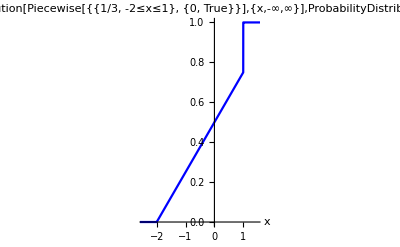

```mathematica
Plot[CDF[ModeloX, x], {x, -3, 2}, PlotRange->{{-2.5, 1.5}, Automatic}, AxesLabel->{x, ModeloX}, PlotStyle->Blue]
```

```mathematica
CDF[ModeloX, x]
```

Piecewise[{{1, x>1}, {(2+x)/4, -2<x<1}, {1/4+(2+x)/4, x==1}, {0, True}}]

```mathematica
fdis5 = CDF[UniformDistribution[{0, 2}], x] (*La variable Y es uniforme en [0, 2]*)
```

Piecewise[{{x/2, 0≤x≤2}, {1, x>2}, {0, True}}]

```mathematica
pdf5=PDF[UniformDistribution[{0, 2}], x]
```

Piecewise[{{1/2, 0≤x≤2}, {0, True}}]

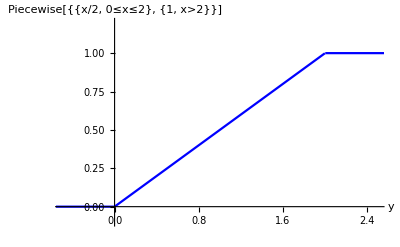

```mathematica
Plot[fdis5, {x, -3, 3}, PlotRange->{{-0.5, 2.5}, {-0.1, 1.2}}, AxesLabel->{y, fdis5}, PlotStyle->Blue](*Convolución de las funciones de distribución;integrando respecto de Y,que es absolutamente continua.*)
```

Función de distribución de la convolución

```mathematica
FConvolucion[z_]:=Convolve[pdf5, CDF[ModeloX, x], x, z]
```

```mathematica
FConvolucion[z]
```

Piecewise[{{1, z≥3}, {(1+z)/4, 0<z≤1}, {1/16 (1+8 z-z^2), 1<z<3}, {1/16 (2+z)^2, -2<z≤0}, {0, True}}]

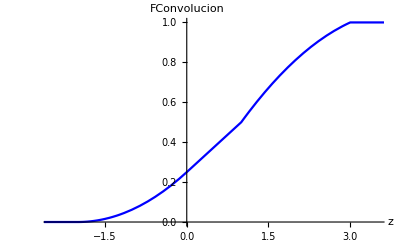

```mathematica
Plot[FConvolucion[z], {z, -3, 4}, PlotRange->{{-2.5, 3.5}, Automatic}, AxesLabel->{z, FConvolucion}, PlotStyle->Blue]
```

Función de distribución de la convolución, mediante la definición.

```mathematica
Integrate[CDF[ModeloX, z-x]*pdf5, {x, 0, 2}]
```

Piecewise[{{1, z>3}, {1/2 (-1+z), z==3}, {(1+z)/4, 0<z≤1}, {1/16 (1+8 z-z^2), 1<z<3}, {1/16 (4+4 z+z^2), -2<z≤0}, {0, True}}]

```mathematica
Simplify[%]
```

Piecewise[{{1, z≥3}, {(1+z)/4, 0<z≤1}, {1/16 (1+8 z-z^2), 1<z<3}, {1/16 (2+z)^2, -2<z≤0}, {0, True}}]

Obtención de las funciones de distribución calculando la distrivuación de la suma de variables

```mathematica
Probability[X+Y<=z, {X\[Distributed]ModeloX, Y\[Distributed]UniformDistribution[{0, 2}]}]
```

Piecewise[{{1, z>3}, {1/2 (-1+z), z==3}, {(1+z)/4, 0<z≤1}, {1/16 (1+8 z-z^2), 1<z<3}, {1/16 (4+4 z+z^2), -2<z≤0}, {0, True}}]

```mathematica
Simplify[%]
```

Piecewise[{{1, z≥3}, {(1+z)/4, 0<z≤1}, {1/16 (1+8 z-z^2), 1<z<3}, {1/16 (2+z)^2, -2<z≤0}, {0, True}}]

Obtención de la función de densidad, a partir de la función de distribución
Función de densidad, derivando la función de distribución

```mathematica
D[FConvolucion[z], z]
```

Piecewise[{{0, z<-2||z==-2}, {(2+z)/8, -2<z<0}, {1/4, z==0||0<z<1}, {1/16 (8-2 z), 1<z<3}, {0, z>3}, {Indeterminate, True}}]

```mathematica
Simplify[%]
```

Piecewise[{{1/4, 0≤z<1}, {(4-z)/8, 1<z<3}, {(2+z)/8, -2<z<0}, {0, z≤-2||z>3}, {Indeterminate, True}}]

```mathematica
FConvolucion'[z] (*concide*)
```

Piecewise[{{0, z<-2||z==-2}, {1/16 (4+2 z), -2<z<0}, {1/4, z==0||0<z<1}, {1/16 (8-2 z), 1<z<3}, {0, z>3}, {Indeterminate, True}}]

```mathematica
Simplify[%]
```

Piecewise[{{1/4, 0≤z<1}, {(4-z)/8, 1<z<3}, {(2+z)/8, -2<z<0}, {0, z≤-2||z>3}, {Indeterminate, True}}]

Definiendo el modelo

```mathematica
ModeloConvolucion=ProbabilityDistribution[{"CDF", FConvolucion[z]}, {z, -∞, ∞}]
```

ProbabilityDistribution[Piecewise[{{1/4, 0<x≤1}, {1/16 (8-2 x), 1<x<3}, {(2+x)/8, -2<x≤0}, {0, True}}],{x,-∞,∞}]

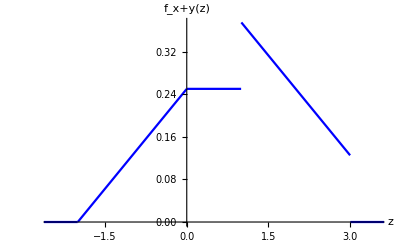

```mathematica
Plot[PDF[ModeloConvolucion, z], {z, -3, 4}, PlotRange->{{-2.5, 3.5}, Automatic}, AxesLabel->{z, f_x+y[z]}, PlotStyle->Blue]
```

Podemos determinar la función de densidad; integrando respecto de X
Determinamos la convolución de la parte continua y la parte discreta de X, y hacemos la mixtura

```mathematica
partediscretaX[x_]:=Piecewise[{{1, x==1}}]
```

```mathematica
partediscretaX[x]
```

Piecewise[{{1, x==1}, {0, True}}]

```mathematica
(3/4)*Convolve[PDF[UniformDistribution[{-2, 1}], x], PDF[UniformDistribution[{0, 2}], x], x, z]+(1/4)*DiscreteConvolve[partediscretaX[x], PDF[UniformDistribution[{0, 2}], x], x, z]
```

1/4 (Piecewise[{{1/2, 1≤z≤3}, {0, True}}])+3/4 (Piecewise[{{1/3, 0<z≤1}, {(3-z)/6, 1<z<3}, {(2+z)/6, -2<z≤0}, {0, True}}])

```mathematica
Simplify[%]
```

Piecewise[{{(4-z)/8, 1≤z≤3}, {1/4, 0<z<1}, {(2+z)/8, -2<z≤0}, {0, True}}]

# Convolución de dos distribuciones mixtas

Funciones de distribución
La variable X es una mixtura de una distribución uniforme en [-1, 1] y una degenerada en 1, con pesos 2/3 y 1/3

```mathematica
ModeloX2=ProbabilityDistribution[{"CDF", Piecewise[{{0, x<-1}, {(x+1)/3, -1<=x<1}, {1, x>=1}}]}, {x, -Infinity, Infinity}]
```

MixtureDistribution[{2/3,1/3},{ProbabilityDistribution[Piecewise[{{1/2, -1≤x≤1}, {0, True}}],{x,-∞,∞}],ProbabilityDistribution[Piecewise[{{1, x==1}, {0, True}}],{x,1,1,1}]}]

La variable Y es una mixtura con pesos 4/7 y 3/7 de una distribución uniforme en [0,2] y una discreta que toma valores 2 y 4 con probabilidades 1/3  y 2/3

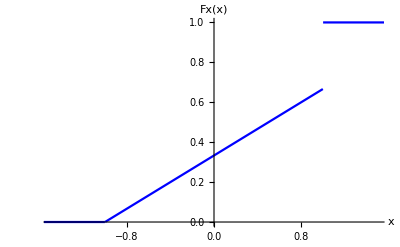

```mathematica
Plot[CDF[ModeloX2, x], {x, -2, 2}, PlotRange->{{-1.5, 1.5}, Automatic}, AxesLabel->{x, Fx[x]}, PlotStyle->Blue]
```

```mathematica
ModeloY2=ProbabilityDistribution[{"CDF", Piecewise[{{0, x<0}, {2*x/7, 0<=x<2}, {5/7, 2<=x<4}, {1, x>=4}}]}, {x, -Infinity, Infinity}]
```

MixtureDistribution[{4/7,3/7},{ProbabilityDistribution[Piecewise[{{1/2, 0≤x<2}, {0, True}}],{x,-∞,∞}],ProbabilityDistribution[Piecewise[{{1/3, x==2}, {2/3, x==4}, {0, True}}],{x,2,4,1}]}]

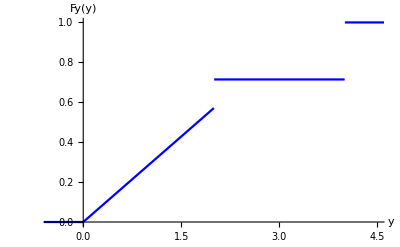

```mathematica
Plot[CDF[ModeloY2, x], {x, -1, 5}, PlotRange->{{-0.5, 4.5}, Automatic}, AxesLabel->{y, Fy[y]}, PlotStyle->Blue]
```

Convolución de las funciones de distribución; integrando respecto de X
Determinamos la convolución de la parte continua y la parte discreta de X, y hacemos la mixtura

```mathematica
(2/3)*Convolve[PDF[UniformDistribution[{-1, 1}],x], Piecewise[{{0, x<0}, {2*x/7, 0<=x<2}, {5/7, 2<=x<4}, {1, x>=4}}], x, z] +  (1/3)*DiscreteConvolve[Piecewise[{{1, x==1}}], Piecewise[{{0, x<0}, {2*x/7, 0<=x<2}, {5/7, 2<=x<4}, {1, x>=4}}], x, z]
```

1/3 (Piecewise[{{5/7, 3≤z<5}, {1, z≥5}, {2/7 (-1+z), 1≤z<3}, {0, True}}])+2/3 (Piecewise[{{1, z>5}, {-5/14 (-5+z), z==3}, {1/2 (-3+z), z==5}, {(2+z)/7, 3<z<5}, {1/14 (3+2 z-z^2), z==1}, {1/14 (-2+7 z-z^2), 1<z<3}, {1/14 (1+2 z+z^2), -1<z<1}, {0, True}}])

```mathematica
Simplify[%]
```

Piecewise[{{1, z≥5}, {1/21 (1+z)^2, -1<z<1}, {1/21 (9+2 z), 3≤z<5}, {1/21 (-4+9 z-z^2), 1≤z<3}, {0, True}}]

Convolución de las funciones de distribución; integrando respecto de Y
Determinamos la convolución de la parte continua y la parte discreta de Y, y hacemos la mixtura

```mathematica
(4/7)*Convolve[PDF[UniformDistribution[{0, 2}], x], Piecewise[{{0, x<-1}, {(x+1)/3, -1<=x<1}, {1, x>=1}}], x, z] + DiscreteConvolve[Piecewise[{{1/7, x==2}, {2/7, x==4}}], Piecewise[{{0, x<-1}, {(x+1)/3, -1<=x<1}, {1, x>=1}}], x, z]
```

(Piecewise[{{3/7, z≥5}, {1/21 (-1+z), 1≤z<3}, {1/21 (-3+2 z), 3≤z<5}, {0, True}}])+4/7 (Piecewise[{{1, z≥3}, {1/12 (-3+8 z-z^2), 1≤z<3}, {1/12 (1+z)^2, -1<z<1}, {0, True}}])

```mathematica
Simplify[%]
```

Piecewise[{{1, z≥5}, {1/21 (1+z)^2, -1<z<1}, {1/21 (9+2 z), 3≤z<5}, {1/21 (-4+9 z-z^2), 1≤z<3}, {0, True}}]

# Problema 4

## Xn = {n(-1+nω) si 0≤ω<1/n, 0 si 1/n ≤ω<2, 1 si 2≤ω<n, n si ω≥n}

Definición de la variable aleatoria mediante una función a trozos

```mathematica
Xn[n_, ω_]:=Piecewise[{{n(n*ω-1), 0<=ω<1/n}, {0, 1/n<=ω<2}, {1, 2<=ω<n}, {n, ω>=n}}]
```

```mathematica
Xn[n, ω]
```

Piecewise[{{n (-1+n ω), 0≤ω<1/n}, {0, 1/n≤ω<2}, {1, 2≤ω<n}, {n, ω≥n}, {0, True}}]

Definición de la probabilidad: P[0, ω] = 1-exp(-λω)

```mathematica
ProbabilidadOmega[λ_, ω_]=CDF[ExponentialDistribution[Xn[n, ω]], ω]
```

Piecewise[{{1-ⅇ^(-ω (Piecewise[{{n (-1+n ω), 0≤ω<1/n}, {0, 1/n≤ω<2}, {1, 2≤ω<n}, {n, ω≥n}, {0, True}}])), ω≥0}, {0, True}}]

Construcción del modelo Fn

```mathematica
Fn[x_, n_, λ_]:=Probability[Xn[n, Omega]<=x, Omega\[Distributed]ExponentialDistribution[λ], Assumptions->n>=3]
```

```mathematica
Fn[x, n, λ]
```

Piecewise[{{1, n-x≤0}, {ⅇ^(-2 λ) (-1+ⅇ^(2 λ)), 0≤x<1}, {ⅇ^(-n λ) (-1+ⅇ^(n λ)), x≥1&&n-x>0}, {ⅇ^(-((n+x) λ)/n^2) (-1+ⅇ^(((n+x) λ)/n^2)), n+x>0&&x<0}, {0, True}}]

```mathematica
Simplify[%]
```

Piecewise[{{1, n≤x}, {1-ⅇ^(-2 λ), 0≤x<1}, {1-ⅇ^(-n λ), x≥1&&n>x}, {1-ⅇ^(-((n+x) λ)/n^2), n+x>0&&x<0}, {0, True}}]

Límite de la sucesión de funciones de distribución y convergencia débil

```mathematica
DiscreteLimit[Fn[x, n, λ], n->∞, Assumptions->λ>0]
```

Piecewise[{{1, x≥1}, {1-ⅇ^(-2 λ), 0≤x<1}, {0, True}}]

Límite de la sucesión de variables aleatorias y convergencia en distribución.

```mathematica
Xlimit[ω_]:=DiscreteLimit[Xn[n, ω], n->∞]
```

```mathematica
Xlimit[w]
```

Piecewise[{{1, w≥2}, {-∞, w==0}, {0, True}}]

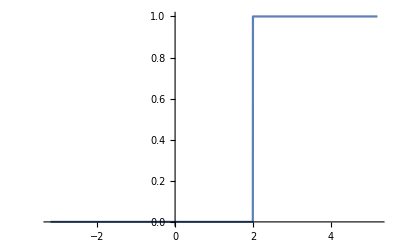

```mathematica
Plot[Xlimit[ω], {ω, -3.2, 5.2}]
```

```mathematica
CDF[TransformedDistribution[Xlimit[Omega], Omega \[Distributed]ExponentialDistribution[λ]], x]
```

Piecewise[{{1, x≥1}, {ⅇ^(-2 λ) (-1+ⅇ^(2 λ)), 0≤x<1}, {0, True}}]

```mathematica
Simplify[%]
```

Piecewise[{{1, x≥1}, {1-ⅇ^(-2 λ), 0≤x<1}, {0, True}}]

Funciones de distribución

```mathematica
Fn[x, n, 1]
```

Piecewise[{{1, n-x≤0}, {(-1+ⅇ^2)/ⅇ^2, 0≤x<1}, {ⅇ^-n (-1+ⅇ^n), x≥1&&n-x>0}, {ⅇ^(-1/n-x/n^2) (-1+ⅇ^(1/n+x/n^2)), n+x>0&&x<0}, {0, True}}]

```mathematica
Fn[x, 3, 1]
```

Piecewise[{{1, x≥3}, {(-1+ⅇ^2)/ⅇ^2, 0≤x<1}, {(-1+ⅇ^3)/ⅇ^3, 1≤x<3}, {ⅇ^(-1/3-x/9) (-1+ⅇ^(1/3+x/9)), -3<x<0}, {0, True}}]

```mathematica
Simplify[%]
```

Piecewise[{{1, x≥3}, {1-1/ⅇ^2, 0≤x<1}, {1-1/ⅇ^3, 1≤x<3}, {1-ⅇ^(-1/3-x/9), -3<x<0}, {0, True}}]

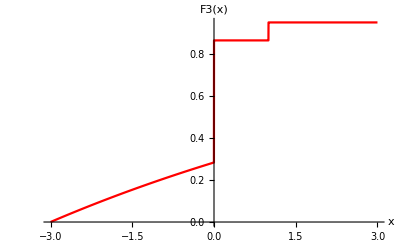

```mathematica
Plot[Fn[x, 3, 1], {x, -3, 3}, PlotStyle->Red, AxesLabel->{x, F3[x]}]
```

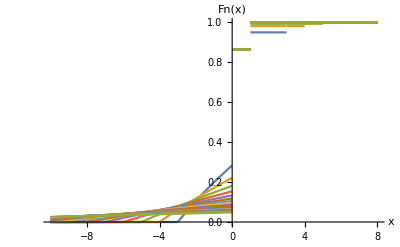

```mathematica
Plot[Evaluate[Table[Fn[x, n, 1], {n, 3, 20}], {x, -10, 8}], AxesLabel->{x, Fn[x]}]
```